# Modeling of the inverse KIE for PCET recombination reaction in [Ru^II-phen-ImN^+H⋯OPh]^(3+)

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/souda/Documents/Projects/Fujita-PCET-H2-evolution/PCET-modeling

```mathematica
Needs["MathPCET`"];
```

The PCET reaction:
 [Ru^II-phen-ImN^+H⋯OPh]^(3+) →^(MV^+)[Ru^II-phen-ImN⋯HOPh]^(2+)

## Parameters

Reorganization energy (kcal/mol):

```mathematica
λ=1.7 ev2au au2kcal
```

39.2031

Reaction free energy (kcal/mol):

```mathematica
dG=-0.98 ev2au au2kcal
```

-22.5994

Electronic coupling (arbitrary) (kcal/mol)

```mathematica
VET=22 cm2au au2kcal
```

0.0629013533

Parameters of the effective donor-acceptor mode:

```mathematica
Meff=7.4664;
Ωeff=333.426255;
RDA=2.61892;
```

```mathematica
Meff Dalton (Ωeff cm2au)^2
```

0.0314127

DH and AH frequencies and dissociation energies:

```mathematica
ωNH=3454.0;
ωOH=2461.0;
```

```mathematica
DNH=93.0;
DOH=102.0;
```

```mathematica
RNH=1.02;
ROH=1.03;
```

```mathematica
?MorseBeta
```

MorseBeta[Omega,DE]
Returns the Morse beta parameter (1/Bohr) corresponding to potential for the vibration with frequency Omega (1/cm).
Parameters:
DE is the dissociation energy in kcal/mol,
Omega is the frequency (1/cm).
Options:
M -> mass of the particle in Daltons.

```mathematica
βNH=MorseBeta[ωNH,DNH,M->MassH]
```

1.23865

```mathematica
βOH=MorseBeta[ωOH,DOH]
```

0.84271

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in MathPCET`Private`time$253608 in the region {{0, ∞}}. NIntegrate obtained 0 and 0 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in MathPCET`Private`time$265618 in the region {{0, ∞}}. NIntegrate obtained 0 and 0 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in MathPCET`Private`time$277628 in the region {{0, ∞}}. NIntegrate obtained 0 and 0 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvi will be suppressed during this calculation.

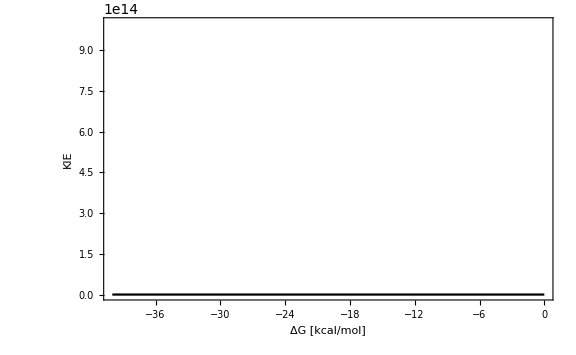

```mathematica
mumax=3;
numax=6;
combined=ListLinePlot[{
Table[{dg,KIEQfluxMorse[VET,dg,λ,Meff,Ωeff,DNH,βNH,DOH,βOH,(RDA-RNH-ROH)a2bohr,300,mumax,numax]},{dg,-40,0,5}],
Table[{dg,KIERhighTMorse[VET,dg,λ,Meff,Ωeff,DNH,βNH,DOH,βOH,(RDA-RNH-ROH)a2bohr,300,mumax,numax]},{dg,-40,0,5}]
},
Axes->False,Frame->True,
PlotStyle->{Black,Red,Blue},
FrameLabel->{"ΔG [kcal/mol]","KIE","{0..3}→{0..6}"},
ImageSize->Large]
```

NIntegrate::precw: The precision of the argument function (2.22843×10^-24\ « 78 »^-« 78 »\ « 28 »^2 + « 66 »\ (1. + Cos[« 79 »\ « 28 »])\ Cos[0.03742426178883577481126820885\ MathPCET`Private`time$570597 + 18.07498068584478545517413294874\ Sin[0.00151920645816424324837934368\ MathPCET`Private`time$570597]]) is less than WorkingPrecision (15.9546).

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in MathPCET`Private`time$572440 in the region {{0, ∞}}. NIntegrate obtained 0 and 0 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (5.5×10^-28\ « 78 »^-« 78 »\ « 28 »^2 + « 68 »\ (1. + Cos[« 79 »\ « 28 »])\ Cos[0.02782084527649347771571797239\ MathPCET`Private`time$577913 + 20.82961546855866430405512801372\ Sin[0.00151920645816424324837934368\ MathPCET`Private`time$577913]]) is less than WorkingPrecision (15.9546).

NIntegrate::precw: The precision of the argument function (2.22843×10^-24\ « 78 »^-« 78 »\ « 28 »^2 + « 66 »\ (1. + Cos[« 79 »\ « 28 »])\ Cos[0.04539226864769607683314234237\ MathPCET`Private`time$585031 + 18.07498068584478545517413294874\ Sin[0.00151920645816424324837934368\ MathPCET`Private`time$585031]]) is less than WorkingPrecision (15.9546).

General::stop: Further output of NIntegrate :: precw will be suppressed during this calculation.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in MathPCET`Private`time$587061 in the region {{0, ∞}}. NIntegrate obtained 0 and 0 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in MathPCET`Private`time$595921 in the region {{0, ∞}}. NIntegrate obtained 3.55086033204584×10^-11 and 5.47991191419409×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvi will be suppressed during this calculation.

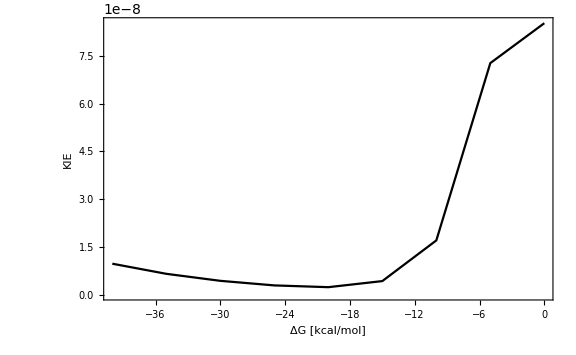

```mathematica
mumax=3;
numax=7;
combined=ListLinePlot[{
Table[{dg,KIEQfluxMorse[VET,dg,λ,Meff,Ωeff,DNH,βNH,DOH,βOH,(RDA-RNH-ROH)a2bohr,300,mumax,numax]},{dg,-40,0,5}]
},
Axes->False,Frame->True,
PlotStyle->{Black,Red,Blue},
FrameLabel->{"ΔG [kcal/mol]","KIE","{0..3}→{0..7}"},
ImageSize->Large]
```

```mathematica
TableRateRhighTMorse[VET,dG,λ,Meff,Ωeff,DNH,βNH,DOH,βOH,(RDA-RNH-ROH)a2bohr,300,3,6]
```

Isotope: 1.01amu; TraditionalForm`ΔG_"00"=-22.6kcal/mol; λ=39.2kcal/mol; M=7.47amu; Ω=333.4cm |  |  |  |  |  |  |  | 
μ | ν | TraditionalForm`P_"\[Mu]" | TraditionalForm`ΔG_"\[Mu]\[Nu]" | ΔG | S | TraditionalForm`"\[Alpha]"_"\[Mu]\[Nu]" | exp(-βΔG) | %
0 | 0 | 1.e |  -22.599 |    1.758 | 3.95392e-5 |   17.445 | 5.2397e-2 |     1.460×10^-29
0 | 1 | 1.e |  -15.806 |    3.491 | 8.78116e-4 |   15.080 | 2.86325e-3 |     5.062×10^-30
0 | 2 | 1.e |   -9.255 |    5.720 | 8.58802e-3 |   12.541 | 6.81388e-5 |     4.058×10^-31
0 | 3 | 1.e |   -2.946 |    8.383 | 4.7257e-2 |    9.753 | 7.82039e-7 |     1.041×10^-32
0 | 4 | 1.e |    3.119 |   11.422 | 1.55879e-1 |    6.591 | 4.77569e-9 |     1.008×10^-34
0 | 5 | 1.e |    8.942 |   14.782 | 3.04117e-1 |    2.816 | 1.70549e-11 |     4.252×10^-37
0 | 6 | 1.e |   14.522 |   18.407 | 3.20751e-1 |   -2.146 | 3.89996e-14 |     9.790×10^-40
1 | 0 | 1.54115e-7 |  -31.951 |    0.335 | 7.25871e-4 |   14.994 | 5.69707e-1 |     1.659×10^-34
1 | 1 | 1.54115e-7 |  -25.157 |    1.258 | 9.91294e-3 |   12.097 | 1.21188e-1 |     1.260×10^-34
1 | 2 | 1.54115e-7 |  -18.606 |    2.705 | 5.52263e-2 |    8.738 | 1.06945e-2 |     2.055×10^-35
1 | 3 | 1.54115e-7 |  -12.298 |    4.616 | 1.49829e-1 |    4.455 | 4.33588e-4 |     9.756×10^-37
1 | 4 | 1.54115e-7 |   -6.232 |    6.932 | 1.76937e-1 |   -2.316 | 8.91005e-6 |     1.919×10^-38
1 | 5 | 1.54115e-7 |   -0.409 |    9.597 | 3.8425e-2 |  -25.452 | 1.02001e-7 |     4.241×10^-37
1 | 6 | 1.54115e-7 |    5.171 |   12.557 | 5.46612e-2 |   26.657 | 7.12256e-10 |     1.056×10^-38
2 | 0 | 5.72345e-14 |  -40.777 |    0.016 | 6.48056e-3 |   12.458 | 9.73835e-1 |     3.703×10^-40
2 | 1 | 5.72345e-14 |  -33.984 |    0.174 | 5.1245e-2 |    8.830 | 7.47223e-1 |     5.654×10^-40
2 | 2 | 5.72345e-14 |  -27.433 |    0.883 | 1.47576e-1 |    4.182 | 2.272e-1 |     1.841×10^-40
2 | 3 | 5.72345e-14 |  -21.125 |    2.084 | 1.57056e-1 |   -3.340 | 3.03161e-2 |     2.356×10^-41
2 | 4 | 5.72345e-14 |  -15.059 |    3.717 | 2.18334e-2 |  -32.536 | 1.9585e-3 |     8.266×10^-37
2 | 5 | 5.72345e-14 |   -9.236 |    5.727 | 4.19311e-2 |   19.093 | 6.73267e-5 |     2.166×10^-42
2 | 6 | 5.72345e-14 |   -3.656 |    8.058 | 6.70655e-2 |  -10.528 | 1.34852e-6 |     1.823×10^-45
3 | 0 | 5.12195e-20 |  -49.080 |    0.622 | 3.52279e-2 |    9.751 | 3.52218e-1 |     2.657×10^-46
3 | 1 | 5.12195e-20 |  -42.286 |    0.061 | 1.42368e-1 |    4.877 | 9.03313e-1 |     7.273×10^-46
3 | 2 | 5.12195e-20 |  -35.735 |    0.077 | 1.6284e-1 |   -2.842 | 8.79297e-1 |     6.128×10^-46
3 | 3 | 5.12195e-20 |  -29.427 |    0.609 | 1.92136e-2 |  -34.701 | 3.59766e-1 |     3.037×10^-39
3 | 4 | 5.12195e-20 |  -23.361 |    1.600 | 4.99461e-2 |   16.642 | 6.826e-2 |     8.301×10^-46
3 | 5 | 5.12195e-20 |  -17.539 |    2.993 | 7.2483e-2 |   -9.557 | 6.60094e-3 |     6.858×10^-48
3 | 6 | 5.12195e-20 |  -11.958 |    4.734 | 3.06818e-3 |   91.892 | 3.5623e-4 |   100.000

```mathematica
TableRateRhighTMorse[VET,dG,λ,Meff,Ωeff,DNH,βNH,DOH,βOH,(RDA-RNH-ROH)a2bohr,300,3,6,M->MassD]
```

Isotope: 2.01amu; TraditionalForm`ΔG_"00"=-22.6kcal/mol; λ=39.2kcal/mol; M=7.47amu; Ω=333.4cm |  |  |  |  |  |  |  | 
μ | ν | TraditionalForm`P_"\[Mu]" | TraditionalForm`ΔG_"\[Mu]\[Nu]" | ΔG | S | TraditionalForm`"\[Alpha]"_"\[Mu]\[Nu]" | exp(-βΔG) | %
0 | 0 | 9.99987e-1 |  -22.599 |    1.758 | 3.1669e-7 |   25.256 | 5.2397e-2 |    50.912
0 | 1 | 9.99987e-1 |  -17.744 |    2.937 | 1.06323e-5 |   22.930 | 7.25745e-3 |    37.668
0 | 2 | 9.99987e-1 |  -13.010 |    4.375 | 1.64285e-4 |   20.489 | 6.49903e-4 |     9.998
0 | 3 | 9.99987e-1 |   -8.398 |    6.052 | 1.52793e-3 |   17.904 | 3.90409e-5 |     1.266
0 | 4 | 9.99987e-1 |   -3.907 |    7.945 | 9.4112e-3 |   15.131 | 1.63082e-6 |     0.086
0 | 5 | 9.99987e-1 |    0.463 |   10.034 | 3.9863e-2 |   12.109 | 4.90579e-8 |     0.003
0 | 6 | 9.99987e-1 |    4.711 |   12.298 | 1.16855e-1 |    8.740 | 1.09954e-9 |     0.000
1 | 0 | 1.26706e-5 |  -29.322 |    0.623 | 8.58908e-6 |   22.846 | 3.519e-1 |     0.028
1 | 1 | 1.26706e-5 |  -24.467 |    1.385 | 2.07967e-4 |   20.189 | 9.79839e-2 |     0.027
1 | 2 | 1.26706e-5 |  -19.733 |    2.418 | 2.24834e-3 |   17.313 | 1.73338e-2 |     0.009
1 | 3 | 1.26706e-5 |  -15.120 |    3.699 | 1.39792e-2 |   14.115 | 2.02143e-3 |     0.001
1 | 4 | 1.26706e-5 |  -10.629 |    5.207 | 5.36201e-2 |   10.404 | 1.61085e-4 |     0.000
1 | 5 | 1.26706e-5 |   -6.260 |    6.921 | 1.25508e-1 |    5.764 | 9.0841e-6 |     5.074×10^-6
1 | 6 | 1.26706e-5 |   -2.011 |    8.821 | 1.61029e-1 |   -1.028 | 3.75084e-7 |     1.701×10^-7

```mathematica
TableRateQfluxMorse[VET,dG,λ,Meff,Ωeff,DNH,βNH,DOH,βOH,(RDA-RNH-ROH)a2bohr,300,5,6]
```

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in MathPCET`Private`time$723647 in the region {{0, ∞}}. NIntegrate obtained 4.43744832592799×10^-12 and 7.7528943967571×10^-16 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in MathPCET`Private`time$728246 in the region {{0, ∞}}. NIntegrate obtained 0 and 0 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (2.×10^-29\ « 78 »^-« 78 »\ « 28 »^2 + « 67 »\ (1. + Cos[« 79 »\ « 28 »])\ Cos[0.02212923587994314322813238505\ MathPCET`Private`time$729695 + 22.02183578092601479170298262034\ Sin[0.00151920645816424324837934368\ MathPCET`Private`time$729695]]) is less than WorkingPrecision (15.9546).

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in MathPCET`Private`time$731326 in the region {{0, ∞}}. NIntegrate obtained 0 and 0 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvi will be suppressed during this calculation.

NIntegrate::precw: The precision of the argument function (2.×10^-29\ « 78 »^-« 78 »\ « 28 »^2 + « 67 »\ (1. + Cos[« 79 »\ « 28 »])\ Cos[0.02212923587994314322813238505\ MathPCET`Private`time$740828 + 22.02183578092601479170298262034\ Sin[0.00151920645816424324837934368\ MathPCET`Private`time$740828]]) is less than WorkingPrecision (15.9546).

Isotope: 1.01amu; TraditionalForm`ΔG_"00"=-22.6kcal/mol; λ=39.2kcal/mol; M=7.47amu; Ω=333.4cm |  |  |  |  |  |  |  | 
μ | ν | TraditionalForm`P_"\[Mu]" | TraditionalForm`ΔG_"\[Mu]\[Nu]" | ΔG | S | TraditionalForm`"\[Alpha]"_"\[Mu]\[Nu]" | exp(-βΔG) | %
0 | 0 | 1.e |  -22.599 |    1.758 | 3.95392e-5 |   17.445 | 5.2397e-2 |     3.856
0 | 1 | 1.e |  -15.806 |    3.491 | 8.78116e-4 |   15.080 | 2.86325e-3 |     1.027
0 | 2 | 1.e |   -9.255 |    5.720 | 8.58802e-3 |   12.541 | 6.81388e-5 |     0.064
0 | 3 | 1.e |   -2.946 |    8.383 | 4.7257e-2 |    9.753 | 7.82039e-7 |     0.001
0 | 4 | 1.e |    3.119 |   11.422 | 1.55879e-1 |    6.591 | 4.77569e-9 |     0.000
0 | 5 | 1.e |    8.942 |   14.782 | 3.04117e-1 |    2.816 | 1.70549e-11 |     3.945×10^-8
0 | 6 | 1.e |   14.522 |   18.407 | 3.20751e-1 |   -2.146 | 3.89996e-14 |     8.972×10^-11
1 | 0 | 1.54115e-7 |  -31.951 |    0.335 | 7.25871e-4 |   14.994 | 5.69707e-1 |     0.000
1 | 1 | 1.54115e-7 |  -25.157 |    1.258 | 9.91294e-3 |   12.097 | 1.21188e-1 |     0.000
1 | 2 | 1.54115e-7 |  -18.606 |    2.705 | 5.52263e-2 |    8.738 | 1.06945e-2 |     2.430×10^-6
1 | 3 | 1.54115e-7 |  -12.298 |    4.616 | 1.49829e-1 |    4.455 | 4.33588e-4 |     9.446×10^-8
1 | 4 | 1.54115e-7 |   -6.232 |    6.932 | 1.76937e-1 |   -2.316 | 8.91005e-6 |     1.765×10^-9
1 | 5 | 1.54115e-7 |   -0.409 |    9.597 | 3.8425e-2 |  -25.452 | 1.02001e-7 |     3.959×10^-7
1 | 6 | 1.54115e-7 |    5.171 |   12.557 | 5.46612e-2 |   26.657 | 7.12256e-10 |     1.233×10^-8
2 | 0 | 5.72345e-14 |  -40.777 |    0.016 | 6.48056e-3 |   12.458 | 9.73835e-1 |     5.703×10^-11
2 | 1 | 5.72345e-14 |  -33.984 |    0.174 | 5.1245e-2 |    8.830 | 7.47223e-1 |     6.680×10^-11
2 | 2 | 5.72345e-14 |  -27.433 |    0.883 | 1.47576e-1 |    4.182 | 2.272e-1 |     1.765×10^-11
2 | 3 | 5.72345e-14 |  -21.125 |    2.084 | 1.57056e-1 |   -3.340 | 3.03161e-2 |     2.210×10^-12
2 | 4 | 5.72345e-14 |  -15.059 |    3.717 | 2.18334e-2 |  -32.536 | 1.9585e-3 |     3.289×10^-6
2 | 5 | 5.72345e-14 |   -9.236 |    5.727 | 4.19311e-2 |   19.093 | 6.73267e-5 |     7.241×10^-13
2 | 6 | 5.72345e-14 |   -3.656 |    8.058 | 6.70655e-2 |  -10.528 | 1.34852e-6 |     2.451×10^-16
3 | 0 | 5.12195e-20 |  -49.080 |    0.622 | 3.52279e-2 |    9.751 | 3.52218e-1 |     3.334×10^-17
3 | 1 | 5.12195e-20 |  -42.286 |    0.061 | 1.42368e-1 |    4.877 | 9.03313e-1 |     7.120×10^-17
3 | 2 | 5.12195e-20 |  -35.735 |    0.077 | 1.6284e-1 |   -2.842 | 8.79297e-1 |     5.683×10^-17
3 | 3 | 5.12195e-20 |  -29.427 |    0.609 | 1.92136e-2 |  -34.701 | 3.59766e-1 |     1.883×10^-8
3 | 4 | 5.12195e-20 |  -23.361 |    1.600 | 4.99461e-2 |   16.642 | 6.826e-2 |     1.988×10^-16
3 | 5 | 5.12195e-20 |  -17.539 |    2.993 | 7.2483e-2 |   -9.557 | 6.60094e-3 |     8.559×10^-19
3 | 6 | 5.12195e-20 |  -11.958 |    4.734 | 3.06818e-3 |   91.892 | 3.5623e-4 |     0.000
4 | 0 | 1.10453e-25 |  -56.858 |    1.988 | 1.22627e-1 |    6.775 | 3.56426e-2 |     9.320×10^-24
4 | 1 | 1.10453e-25 |  -50.064 |    0.752 | 1.94192e-1 |   -0.829 | 2.83115e-1 |     4.070×10^-23
4 | 2 | 1.10453e-25 |  -43.513 |    0.118 | 3.09464e-2 |  -26.230 | 8.19759e-1 |     2.642×10^-17
4 | 3 | 1.10453e-25 |  -37.205 |    0.025 | 4.70323e-2 |   17.598 | 9.58203e-1 |     1.574×10^-20
4 | 4 | 1.10453e-25 |  -31.140 |    0.415 | 6.73373e-2 |  -10.567 | 4.98828e-1 |     2.115×10^-22
4 | 5 | 1.10453e-25 |  -25.317 |    1.230 | 8.71359e-3 |   57.028 | 1.27116e-1 |    95.051
4 | 6 | 1.10453e-25 |  -19.737 |    2.417 | 7.02703e-2 |   -4.672 | 1.73617e-2 |     1.329×10^-24
5 | 0 | 5.73968e-31 |  -64.112 |    3.957 | 2.67724e-1 |    3.368 | 1.31111e-3 |     1.769×10^-30
5 | 1 | 5.73968e-31 |  -57.318 |    2.093 | 7.38673e-2 |  -15.001 | 2.98883e-2 |     1.580×10^-27
5 | 2 | 5.73968e-31 |  -50.767 |    0.853 | 3.62608e-2 |   22.929 | 2.39187e-1 |     3.110×10^-24
5 | 3 | 5.73968e-31 |  -44.459 |    0.176 | 7.7467e-2 |   -8.488 | 7.44155e-1 |     9.946×10^-28
5 | 4 | 5.73968e-31 |  -38.393 |    0.004 | 7.50155e-3 |   60.923 | 9.93014e-1 |     0.000
5 | 5 | 5.73968e-31 |  -32.571 |    0.281 | 6.00198e-2 |   -6.845 | 6.24661e-1 |     3.538×10^-28
5 | 6 | 5.73968e-31 |  -26.990 |    0.951 | 6.6526e-3 |   68.477 | 2.02825e-1 |     0.000

```mathematica
?KIEUKHarmonic
```

KIEUKHarmonic[V_,DG_,lambda_,MR_,FR_,f1_,f2_,d_,T_,mumax_,numax_]:
Parameters:
V - electronic coupling (kcal/mol),
DG - reaction free energy (free energy bias) (kcal/mol),
lambda - solvent reorganization energy (kcal/mol),
f1 - frequency of the left (proton donor) protium oscillator,
f2 - frequency of the right (proton acceptor) protium oscillator,
MR - reduced mass of the donor-acceptor mode (Dalton),
FR - donor-acceptor mode frequency (1/cm),
d - equilibrium distance between the minima of the proton potentials (Bohr),
T - temperature (K),
mumax, numax - highest quantum numbers for the left and right oscillators states, respectively.
Options:
M1,M2->masses of the particle in Daltons (Default - protium and deuterium),
Distribution->
Classical or Quantal (for R-oscillator distribution function).

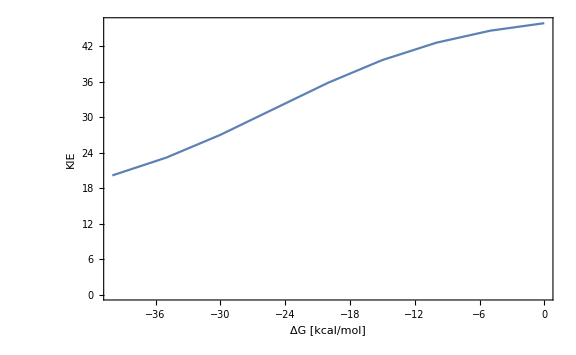

```mathematica
UKharmonic=ListLinePlot[Table[{dg,KIEUKHarmonic[VET,dg,λ,Meff,Ωeff,ωNH,ωOH,(RDA-RNH-ROH)a2bohr,300,6,6,Distribution->"Quantal"]},{dg,-40,0,5}],
Axes->False,Frame->True,
FrameLabel->{"ΔG [kcal/mol]","KIE","UKharmonic(6,6)"},
ImageSize->Large]
```

```mathematica
?TableRateUKHarmonic
```

TableRateUKHarmonic[V_,DG_,lambda_,MR_,FR_,f1_,f2_,d_,T_,mumax_,numax_]:
Parameters:
V - electronic coupling (kcal/mol),
DG - reaction free energy (free energy bias) (kcal/mol),
lambda - solvent reorganization energy (kcal/mol),
f1 - frequency of the left (proton donor) oscillator,
f2 - frequency of the right (proton acceptor) oscillator,
MR - reduced mass of the donor-acceptor mode (Dalton),
FR - donor-acceptor mode frequency (1/cm),
d - equilibrium distance between the minima of the proton potentials (Bohr),
T - temperature (K),
mumax, numax - highest quantum numbers for the left and right oscillators states, respectively.
Options:
M->mass of the particle in Daltons (Default - protium),
Distribution->
Classical or Quantal (for R-oscillator distribution function).

```mathematica
TableRateUKHarmonic[VET,dG,λ,Meff,Ωeff,ωNH,ωOH,(RDA-RNH-ROH)a2bohr,300,6,6,M->MassH]
```

Isotope: 2.01amu; TraditionalForm`ΔG_"00"=-22.6kcal/mol; λ=39.2kcal/mol; M=7.47amu; Ω=333.4cm |  |  |  |  |  |  | 
μ | ν | TraditionalForm`P_"\[Mu]" | TraditionalForm`ΔG_"\[Mu]\[Nu]" | ΔG | <S> | exp(-βΔG) | %
0 | 0 | 3.95421e3 |  -22.599 |    1.758 | 7.6236e-6 | 5.2397e-2 |    77.337
0 | 1 | 3.95421e3 |  -15.562 |    3.564 | 4.37179e-5 | 2.53228e-3 |    21.433
0 | 2 | 3.95421e3 |   -8.524 |    6.002 | 1.47451e-4 | 4.24152e-5 |     1.211
0 | 3 | 3.95421e3 |   -1.486 |    9.072 | 3.77819e-4 | 2.46227e-7 |     0.018
0 | 4 | 3.95421e3 |    5.552 |   12.773 | 8.10713e-4 | 4.95398e-10 |     0.000
0 | 5 | 3.95421e3 |   12.590 |   17.106 | 1.53165e-3 | 3.45443e-13 |     1.024×10^-7
0 | 6 | 3.95421e3 |   19.627 |   22.071 | 2.62534e-3 | 8.34842e-17 |     4.243×10^-11
1 | 0 | 2.52289e-4 |  -32.476 |    0.289 | 3.11493e-5 | 6.16304e-1 |     0.000
1 | 1 | 2.52289e-4 |  -25.439 |    1.208 | 1.55077e-4 | 1.31778e-1 |     0.000
1 | 2 | 2.52289e-4 |  -18.401 |    2.760 | 4.6042e-4 | 9.76558e-3 |     0.000
1 | 3 | 2.52289e-4 |  -11.363 |    4.943 | 1.04762e-3 | 2.50816e-4 |     3.246×10^-6
1 | 4 | 2.52289e-4 |   -4.325 |    7.757 | 2.00886e-3 | 2.23264e-6 |     5.540×10^-8
1 | 5 | 2.52289e-4 |    2.713 |   11.204 | 3.40866e-3 | 6.88788e-9 |     2.900×10^-10
1 | 6 | 2.52289e-4 |    9.750 |   15.282 | 5.27e-3 | 7.36474e-12 |     4.794×10^-13
2 | 0 | 1.60967e-11 |  -42.353 |    0.063 | 8.38641e-5 | 8.99285e-1 |     5.944×10^-11
2 | 1 | 1.60967e-11 |  -35.315 |    0.096 | 3.7081e-4 | 8.50728e-1 |     2.486×10^-10
2 | 2 | 1.60967e-11 |  -28.278 |    0.761 | 9.92984e-4 | 2.78926e-1 |     2.183×10^-10
2 | 3 | 1.60967e-11 |  -21.240 |    2.058 | 2.05793e-3 | 3.1695e-2 |     5.141×10^-11
2 | 4 | 1.60967e-11 |  -14.202 |    3.986 | 3.6201e-3 | 1.24824e-3 |     3.561×10^-12
2 | 5 | 1.60967e-11 |   -7.164 |    6.546 | 5.66719e-3 | 1.70376e-5 |     7.610×10^-14
2 | 6 | 1.60967e-11 |   -0.126 |    9.738 | 8.1225e-3 | 8.05981e-8 |     5.160×10^-16
3 | 0 | 1.02702e-18 |  -52.230 |    1.082 | 1.82464e-4 | 1.62785e-1 |     1.494×10^-18
3 | 1 | 1.02702e-18 |  -45.192 |    0.229 | 7.2497e-4 | 6.81321e-1 |     2.484×10^-17
3 | 2 | 1.02702e-18 |  -38.155 |    0.007 | 1.77294e-3 | 9.88311e-1 |     8.811×10^-17
3 | 3 | 1.02702e-18 |  -31.117 |    0.417 | 3.38939e-3 | 4.96867e-1 |     8.468×10^-17
3 | 4 | 1.02702e-18 |  -24.079 |    1.459 | 5.54017e-3 | 8.65747e-2 |     2.412×10^-17
3 | 5 | 1.02702e-18 |  -17.041 |    3.132 | 8.10597e-3 | 5.22813e-3 |     2.131×10^-18
3 | 6 | 1.02702e-18 |  -10.003 |    5.437 | 1.09118e-2 | 1.09422e-4 |     6.004×10^-20
4 | 0 | 6.55264e-26 |  -62.107 |    3.345 | 3.46553e-4 | 3.65549e-3 |     4.064×10^-27
4 | 1 | 6.55264e-26 |  -55.069 |    1.605 | 1.24647e-3 | 6.76903e-2 |     2.707×10^-25
4 | 2 | 6.55264e-26 |  -48.032 |    0.497 | 2.8063e-3 | 4.34423e-1 |     3.911×10^-24
4 | 3 | 6.55264e-26 |  -40.994 |    0.020 | 4.98967e-3 | 9.66281e-1 |     1.547×10^-23
4 | 4 | 6.55264e-26 |  -33.956 |    0.176 | 7.64161e-3 | 7.44901e-1 |     1.826×10^-23
4 | 5 | 6.55264e-26 |  -26.918 |    0.962 | 1.05373e-2 | 1.99021e-1 |     6.728×10^-24
4 | 6 | 6.55264e-26 |  -19.880 |    2.381 | 1.34356e-2 | 1.8429e-2 |     7.944×10^-25
5 | 0 | 4.18076e-33 |  -71.984 |    6.853 | 5.975e-4 | 1.01833e-5 |     1.246×10^-36
5 | 1 | 4.18076e-33 |  -64.946 |    4.226 | 1.9556e-3 | 8.34288e-4 |     3.340×10^-34
5 | 2 | 4.18076e-33 |  -57.909 |    2.231 | 4.07729e-3 | 2.3689e-2 |     1.977×10^-32
5 | 3 | 4.18076e-33 |  -50.871 |    0.868 | 6.78339e-3 | 2.33121e-1 |     3.237×10^-31
5 | 4 | 4.18076e-33 |  -43.833 |    0.137 | 9.79336e-3 | 7.95097e-1 |     1.594×10^-30
5 | 5 | 4.18076e-33 |  -36.795 |    0.037 | 1.28065e-2 | 9.39862e-1 |     2.464×10^-30
5 | 6 | 4.18076e-33 |  -29.757 |    0.569 | 1.55639e-2 | 3.85046e-1 |     1.227×10^-30
6 | 0 | 2.66744e-40 |  -81.861 |   11.604 | 9.57072e-4 | 3.51925e-9 |     4.399×10^-47
6 | 1 | 2.66744e-40 |  -74.823 |    8.091 | 2.86168e-3 | 1.27561e-6 |     4.768×10^-44
6 | 2 | 2.66744e-40 |  -67.785 |    5.210 | 5.55097e-3 | 1.60248e-4 |     1.162×10^-41
6 | 3 | 2.66744e-40 |  -60.748 |    2.960 | 8.68308e-3 | 6.97706e-3 |     7.912×10^-40
6 | 4 | 2.66744e-40 |  -53.710 |    1.342 | 1.18758e-2 | 1.05282e-1 |     1.633×10^-38
6 | 5 | 2.66744e-40 |  -46.672 |    0.356 | 1.48009e-2 | 5.5061e-1 |     1.064×10^-37
6 | 6 | 2.66744e-40 |  -39.634 |    0.001 | 1.72327e-2 | 9.98013e-1 |     2.246×10^-37